Number of eigenvalues: 10000

Erste 12 Eigenwerte (gerundet):

{40.5750,43.8649,49.3480,49.3480,57.0244,63.6041,66.8940,78.9568,80.0535,89.9231,93.2129,93.2129}

Last 4 eigenvalues:

{42430.5259,42440.3955,42440.3955,42440.3955}

--- Schritt 1: Fläche ---

Rekonstruierte Fläche A = a*b ≈ 2.9614 (Wahr: 3.0)

--- Schritt 2: Fourier-Analyse (Bestimmung der Längen L = 2a, 2b) ---

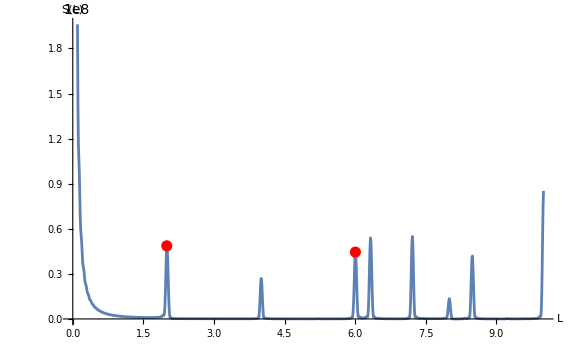

Gefundene Längen L = 2*a, 2*b ≈ (1.9968, 6.0032)

Rekonstruierte Seitenlängen (a, b) ≈ (0.9984, 3.0016)

Bester Fit für Seitenverhältnis R = a/b ≈ 0.3326

--- Schritt 3: Endergebnis ---

Rekonstruierte Seitenlängen (geordnet): (a, b) ≈ (0.9984, 3.0016)

Wahre Seitenlängen (geordnet): (a, b) = (1.0, 3.0)

```mathematica
ClearAll[aTrue,bTrue,reconstructAspectRatioFourierAnalysis];

aTrue=1.0;
bTrue=3.0;
pi=Pi;

(* Eigenwerte des Rechtecks generieren *)
mMax=800;
nMax=800;
ms=Range[1,mMax];
ns=Range[1,nMax];

lambdas=Table[Pi^2 (m^2/aTrue^2+n^2/bTrue^2),{m,ms},{n,ns}];
lFlat=Flatten[lambdas];
lSorted=Sort[lFlat];

Nvals=10000;
(* überspringt die ersten 5 *)
startIndex=6;
endIndex=startIndex+Nvals-1;
eigvals=lSorted[[startIndex;;endIndex]];
numVals=Length[eigvals];
Print["Number of eigenvalues: ",numVals];
Print["Erste 12 Eigenwerte (gerundet):"];
Print[NumberForm[#,{Infinity,4}]&/@Take[eigvals,12]];
Print["Last 4 eigenvalues:"];
Print[NumberForm[#,{Infinity,4}]&/@Take[eigvals,-4]];

reconstructAspectRatioFourierAnalysis[eigvals_List,NtotalFit_:9500]:=Module[{
(* Basisgrößen *)
Ntotal,vals,kVals,startIndexA,subVals,subK,lm,slopeA,Ahat,tK,Nweyl,Fk,weight,FkW,
(* Spektraldichte, 1024 Punkte–reicht für den Start *)
Lmax=10.0,Nfft=2^10,Laxis,spectralDensity,specFun,
(* Peaks/Längen *)
len,idxMin,specSub,idxTopSub,peakIdx,L1hat,L2hat,Lshort,Llong,aHat,bHat,Rhat,aTrueFinal,bTrueFinal},

(* Begrenze Ntotal für Performance *)
Ntotal=Min[Length[eigvals],NtotalFit,4000];
vals=Developer`ToPackedArray@N[Take[eigvals,Ntotal]];
kVals=Range[1,Ntotal];


(* 1. Schritt: Fläche A via Weyl-Fit *)
Print["--- Schritt 1: Fläche ---"];
startIndexA=Floor[0.3 Ntotal];
subVals=vals[[startIndexA;;]];
subK=kVals[[startIndexA;;]];

(* lineare Regression:k≈β0+β1 λ *)
lm=LinearModelFit[Transpose[{subVals,subK}],x,x];
slopeA=lm["BestFitParameters"][[2]];
Ahat=4 Pi slopeA;
Print["Rekonstruierte Fläche A = a*b ≈ ",NumberForm[Ahat,{Infinity,4}]," (Wahr: ",NumberForm[aTrue*bTrue,{Infinity,1}],")"];


(* 2. Schritt: Spektrale Fluktuationen *)Print["\n--- Schritt 2: Fourier-Analyse (Bestimmung der Längen L = 2a, 2b) ---"];
tK=Developer`ToPackedArray@Sqrt[vals];
Nweyl=(Ahat/(4 Pi)) vals;
Fk=Developer`ToPackedArray@(kVals-Nweyl);
(* Gewichtung (Gauss) *)
weight=Developer`ToPackedArray@Exp[-1/2 (tK/Last[tK])^2];
FkW=Developer`ToPackedArray@N[Fk*weight];
(* Kompilierte Spektraldichte-Funktion: S(L)= |Sum_k FkW_k*exp(-i L t_k)|^2->Real/Imaginär-Teile explizit *)specFun=Compile[{{L,_Real},{tKc,_Real,1},{FkWc,_Real,1}},Module[{sRe=0.,sIm=0.,arg,c,s,lenLocal},lenLocal=Length[tKc];
Do[arg=L*tKc[[k]];
c=Cos[arg];
s=Sin[arg];
(* FkW*(cos-i sin) *)
sRe+=FkWc[[k]]*c;
sIm+=-FkWc[[k]]*s;,{k,1,lenLocal}];
sRe^2+sIm^2],CompilationTarget->"WVM",RuntimeOptions->"Speed"];
(* L-Achse *)
Laxis=Subdivide[0.1,Lmax,Nfft-1];
spectralDensity=Developer`ToPackedArray@(specFun[#,tK,FkW]&/@Laxis);

(* Peaks=Top-2-Maxima der Spektraldichte, Peaks über lokale Maxima+Flächenkriterium *)
len=Length[spectralDensity];
(* sehr kleine L-Werte ignorieren *)
idxMin=Round[0.05 len];
(* Wir prüfen i=2 bis len−1, weil wir für einen lokalen Peak immer zwei Nachbarn brauchen *)
localMaxIdx=Select[
Range[2,len-1],
spectralDensity[[#]]>spectralDensity[[#-1]]&&spectralDensity[[#]]>=spectralDensity[[#+1]]&];

(* nur Maxima jenseits idxMin *)
localMaxIdx=Select[localMaxIdx,#>=idxMin&];

If[Length[localMaxIdx]<2,Print["Warnung: Zu wenige lokale Maxima, nehme wieder einfache Top-2."];(* Fallback: zwei größten Werte im Bereich[idxMin;;len] *)
specSub=spectralDensity[[idxMin;;]];
idxTopSub=Ordering[specSub,-2];
peakIdx=idxMin-1+idxTopSub;,

(* Sonst:aus lokalen Maxima die beste Paar-Kombination nach Flächenkriterium wählen *)
(* Schwelle: nur „starke“ Peaks *)
Module[{threshold,strongIdx,pairs,minSep,areaTarget,areaErrors,best},threshold=0.1 Max[spectralDensity];
strongIdx=Select[localMaxIdx,spectralDensity[[#]]>=threshold&];
(* Wenn nach Threshold zu wenig übrig bleibt,nimm alle lokalen Maxima *)
If[Length[strongIdx]<2, strongIdx=localMaxIdx;];
(* Alle möglichen Paare *)
pairs=Subsets[strongIdx,{2}];
(* Mindestabstand der Peaks in Index-Space *)
minSep=Round[0.05 len];
pairs=Select[pairs,Abs[#[[1]]-#[[2]]]>=minSep&];
(* Falls alles rausgefiltert wurde, nimm wieder simple Top-2 der starken *)
If[Length[pairs]<1,pairs=Subsets[strongIdx,{2}];];
(* A≈a*b *)
areaTarget=Ahat;areaErrors=Table[Module[{i1=p[[1]],i2=p[[2]],L1=Laxis[[p[[1]]]],L2=Laxis[[p[[2]]]],aCand,bCand,areaCand},aCand=L1/2.;
bCand=L2/2.;
areaCand=aCand*bCand;
Abs[areaCand-areaTarget]],{p,pairs}];
best=First@Ordering[areaErrors,1];
peakIdx=pairs[[best]];];];

(* Jetzt haben wir genau zwei Indizes *)
L1hat=Laxis[[peakIdx[[1]]]];
L2hat=Laxis[[peakIdx[[2]]]];

(* Peak-Plot zur Kontrolle *)peakPlot=Show[ListLinePlot[Transpose[{Laxis,spectralDensity}],PlotRange->All,AxesLabel->{"L","S(L)"},ImageSize->Large],ListPlot[{{Laxis[[peakIdx[[1]]]],spectralDensity[[peakIdx[[1]]]]},{Laxis[[peakIdx[[2]]]],spectralDensity[[peakIdx[[2]]]]}},PlotStyle->{Red,AbsolutePointSize[8]}]];
Print[peakPlot];

{Lshort,Llong}=Sort[{L1hat,L2hat}];
aHat=Lshort/2.0;
bHat=Llong/2.0;
Print["Gefundene Längen L = 2*a, 2*b ≈ (",NumberForm[Lshort,{Infinity,4}],", ",NumberForm[Llong,{Infinity,4}],")"];
Print["Rekonstruierte Seitenlängen (a, b) ≈ (",NumberForm[aHat,{Infinity,4}],", ",NumberForm[bHat,{Infinity,4}],")"];

(* 3. Schritt: Endergebnis *)
Rhat=aHat/bHat;
Print["Bester Fit für Seitenverhältnis R = a/b ≈ ",NumberForm[Rhat,{Infinity,4}]];
Print["\n--- Schritt 3: Endergebnis ---"];
{aTrueFinal,bTrueFinal}=Sort[{aTrue,bTrue}];
Print["Rekonstruierte Seitenlängen (geordnet): (a, b) ≈ (",NumberForm[aHat,{Infinity,4}],", ",NumberForm[bHat,{Infinity,4}],")"];
Print["Wahre Seitenlängen (geordnet): (a, b) = (",NumberForm[aTrueFinal,{Infinity,1}],", ",NumberForm[bTrueFinal,{Infinity,1}],")"];
{aHat,bHat,Rhat}];

(*Aufruf*)
{aRec,bRec,RRec}=reconstructAspectRatioFourierAnalysis[eigvals];
```